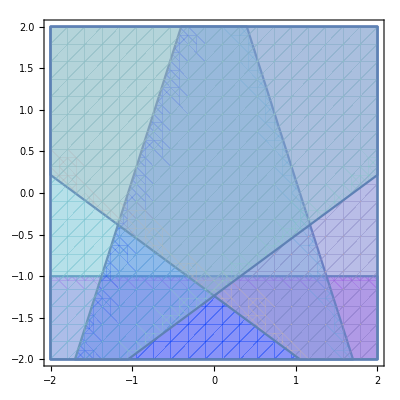

-Graphics-

```mathematica
(*We can show abstain on 5 outcomes is not 2-embeddable using normals were in the shape of a uniform star (and polytope is a pentagon)*)
V = {{0,1}, {Sin[2Pi / 5], Cos[2 Pi / 5]}, {-Sin[2Pi / 5], Cos[2 Pi / 5]}, {-Sin[4Pi / 5], -Cos[ Pi / 5]}, {Sin[4Pi / 5], -Cos[ Pi / 5]}};

B = {{-1,1,1,1,1}, {1,-1,1,1,1}, {1,1,-1,1,1}, {1,1,1,-1,1}, {1,1,1,1,-1}};

Show[MapIndexed[RegionPlot[#1 . {x1, x2} ≤ B[[1]][[#2]][[1]], {x1, -2,2}, {x2,-2,2}, PlotStyle->{RandomColor[], Opacity[0.3]}]&, V]] (*Plots all of the regions together-- you can see there's no overlap over all 5 regions, and i.e. no feasible solution.*)


polytopenumber = 1; (*Think of this as report number, feel free to change to see if there was a polytope for each.  *)
RegionPlot[Intersection[MapIndexed[#1 . {x1, x2} ≤ B[[polytopenumber]][[#2]][[1]]&, V]], {x1, -2,2}, {x2,-2,2}, PlotStyle->{RandomColor[], Opacity[0.3]}] (*T_i for report i=polytopenumber*)
(*Shows that a set of normals forming a regular pentagon doesn't work*)
```

```mathematica
(*2D CASE-- GENERAL.  I.e. no assumptions on V*)
```

```mathematica
V2 = {{v11, v12}, {v21,v22}, {v31,v32}, {v41,v42}, {v51,v52}}; (*General set of normals*)
X2 = {{x121,x122}, {x231,x232}, {x341,x342}, {x451,x452}, {x511,x512}};

qpfcons1 = V2[[1]] . X2[[1]] == 1 && V2[[2]] . X2[[2]] == 1 && V2[[3]] . X2[[3]] == 1 && V2[[4]] . X2[[4]] == 1 && V2[[5]] . X2[[5]] == 1;
qpfcons2 = V2[[1]] . X2[[5]] == 1 && V2[[2]] . X2[[1]] == 1 && V2[[3]] . X2[[2]] == 1 && V2[[4]] . X2[[3]] == 1 && V2[[5]] . X2[[4]] == 1;
qpfcons3 = V2[[1]] . X2[[2]] ≤  -1 && V2[[2]] . X2[[3]] ≤ -1 && V2[[3]] . X2[[4]] ≤ -1 && V2[[4]] . X2[[5]] ≤ -1 && V2[[5]]. X2[[1]] ≤ - 1;
qpfcons4 = V2[[1]] . X2[[4]] ≤  1 && V2[[2]] . X2[[5]] ≤ 1 && V2[[3]] . X2[[1]] ≤ 1 && V2[[4]] . X2[[2]] ≤ 1 && V2[[5]]. X2[[3]] ≤  1;
FindInstance[And[qpfcons1, qpfcons2, qpfcons3, qpfcons4], Join[Flatten[V2],Flatten[X2]]] (*This line yielding an output would give a set of normals and x's such that abstain on 5 outcomes is 2-embeddable... running a solve on this input gives no solution after a long time, so that's further support that abstain isn't 2-embeddable. *)
```

```mathematica
(*3D CASESTARTS HERE*)
```

```mathematica
V3 = {{0,-1,-1}, {2,-1,-1}, {0,0,1}, {-2,0,1}, {0,0,-1}};
(*V3= {{v11, v12,v13}, {v21,v22,v23}, {v31,v32,v33}, {v41,v42,v43}, {v51,v52,v53}};*) (*This line is used to find the previous via the first FindInstance call, currently commented out*)
x12 = {x121,x122,x123} ;
x23 = {x231,x232,x233} ;
x34 = {x341,x342,x343} ;
x45 = {x451,x452,x453} ;
x51 = {x511,x512,x513} ;
X3 = {x12, x23,x34,x45,x51};

qpfcons1 = V3[[1]] . X3[[1]] == 1 && V3[[2]] . X3[[2]] == 1 && V3[[3]] . X3[[3]] == 1 && V3[[4]] . X3[[4]] == 1 && V3[[5]]. X3[[5]] == 1;
qpfcons2 = V3[[1]] . X3[[5]] == 1 && V3[[2]] . X3[[1]] == 1 && V3[[3]] . X3[[2]] == 1 && V3[[4]] . X3[[3]] == 1 && V3[[5]]. X3[[4]] == 1;
qpfcons3 = V3[[1]] . X3[[2]] ≤  -1 && V3[[2]] . X3[[3]] ≤ -1 && V3[[3]] . X3[[4]] ≤ -1 && V3[[4]] . X3[[5]] ≤ -1 && V3[[5]]. X3[[1]] ≤ - 1;
qpfcons4 = V3[[1]] . X3[[4]] ≤  1 && V3[[2]] . X3[[5]] ≤ 1 && V3[[3]] . X3[[1]] ≤ 1 && V3[[4]] . X3[[2]] ≤ 1 && V3[[5]]. X3[[3]] ≤  1;
(*FindInstance[And[qpfcons1,qpfcons2, qpfcons3, qpfcons4], Join[Flatten[V3], Flatten[X3]]]*) (*Uncomment this and the second V3 line to see how I found the first V3 line*)
FindInstance[And[qpfcons1,qpfcons2, qpfcons3, qpfcons4], Flatten[X3]]
(*Solve[And[qpfcons1,qpfcons2, qpfcons3, qpfcons4]]*)(*Takes forever and a year*)
```

```mathematica
polytopenumber = 1; (*Change this in order to see the subgradient sets associated with each of the five reports (i.e. this is the report number) *)

RegionPlot3D[Reduce[And[Intersection[MapIndexed[(V3 . {x1,x2,x3})[[polytopenumber]] ≤ B[[polytopenumber]][[#1]]&, Range[5]]]]], {x1,-5,5}, {x2,-5,5}, {x3,-5,5}, PlotStyle->{RandomColor[], Opacity[0.]}] (*T_i for i=polytopenumber and we can see none of these are empty.*)
```

-Graphics3D-